```mathematica
γ=0.1;
eq=D[B[τ],{τ,2}]+ⅈ*γ*τ*D[B[τ],τ]+γ^2*B[τ]==0;
initialConditions={B[-1000]==1,B'[-1000]==0};

sol=NDSolve[{eq,initialConditions},B,{τ,-100,100}]
```

{{B→InterpolatingFunction[…]}}

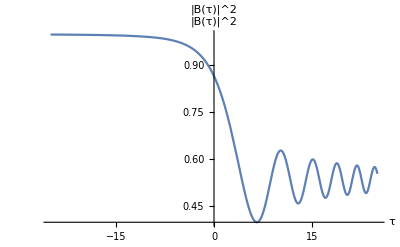

```mathematica
plot=Plot[Abs[B[τ]]^2/.sol,{τ,-25,25},PlotRange->All,PlotLabel->"|B(τ)|^2",AxesLabel->{"τ","|B(τ)|^2"}]
```

```mathematica
longTimeLimit=Abs[B[100]]^2/.First[sol]
```

0.537657